## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="FBP2";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data_model.csv";

mainFolder = "fit_FBP2";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction];
```

(fdp^c+h2o^c→f6p^c+pi^c)^FBP2

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp,Null | 41.5 | 39.425
43.575 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00007 | 0.000068
0.000072 |  | M | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 5.7 | 5.6
5.8 | 1/s | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | f1p | 0.001 | 0.00095
0.00105 |  | Competitive | fdp | 0.00007 | M | 7.7 | 25 | tric | 0.02 | mn2 | 0.001
cl | 0.002
1 | Kic | pi | 0.00035 | 0.0003325
0.0003675 |  | Competitive | fdp | 0.00007 | M | 7.7 | 25 | tric | 0.02 | mn2 | 0.001
cl | 0.002

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | n | fdp | 2.05 | 2.
2.1 |  |  |  |  |  |

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {};
s05Priorities = {1};
kcatPriorities = {0};
inhibitionPriorities={0,0};
activationPriorities = Null;
otherParamsPriorities = {1};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(fdp^c+h2o^c→f6p^c+pi^c)^FBP2

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp,Null | 41.5 | 39.425
43.575 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00007 | 0.000068
0.000072 |  | M | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | n | fdp | 2.05 | 2.
2.1 |  |  |  |  |  |

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

```mathematica
catalyticBranch={"E_FBP2[c] + fdp[c] <=> E_FBP2[c]&fdp",
				"E_FBP2[c]&fdp <=> E_FBP2[c]&f6p&pi",

				"E_FBP2[c]&f6p&pi <=> E_FBP2[c]&f6p + pi[c]",
				"E_FBP2[c]&f6p <=> E_FBP2[c] + f6p[c]",
				
				"E_FBP2[c]&f6p&pi <=> E_FBP2[c]&pi + f6p[c]",
				"E_FBP2[c]&pi <=> E_FBP2[c] + pi[c]",

"E_FBP2[c] + fdp[c] <=> E_FBP2[c]&fdp",
				"E_FBP2[c]&fdp <=> E_FBP2[c]&f6p&pi",

				"E_FBP2[c]&f6p&pi <=> E_FBP2[c]&f6p + pi[c]",
				"E_FBP2[c]&f6p <=> E_FBP2[c] + f6p[c]",
				
				"E_FBP2[c]&f6p&pi <=> E_FBP2[c]&pi + f6p[c]",
				"E_FBP2[c]&pi <=> E_FBP2[c] + pi[c]"};



enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((FBP2^c)_^+fdp^c⇌(FBP2^c&fdp^c)_^)^FBP21,((FBP2^c)_^+fdp^c⇌(FBP2^c&fdp^c)_^)^FBP22,((FBP2^c&pi^c)_^⇌(FBP2^c)_^+pi^c)^FBP23,((FBP2^c&f6p^c)_^⇌(FBP2^c)_^+f6p^c)^FBP24,((FBP2^c&fdp^c)_^⇌(FBP2^c&f6p^c&pi^c)_^)^FBP25,((FBP2^c&pi^c)_^⇌(FBP2^c)_^+pi^c)^FBP26,((FBP2^c&f6p^c)_^⇌(FBP2^c)_^+f6p^c)^FBP27,((FBP2^c&fdp^c)_^⇌(FBP2^c&f6p^c&pi^c)_^)^FBP28,((FBP2^c&f6p^c&pi^c)_^⇌(FBP2^c&pi^c)_^+f6p^c)^FBP29,((FBP2^c&f6p^c&pi^c)_^⇌(FBP2^c&f6p^c)_^+pi^c)^FBP210,((FBP2^c&f6p^c&pi^c)_^⇌(FBP2^c&pi^c)_^+f6p^c)^FBP211,((FBP2^c&f6p^c&pi^c)_^⇌(FBP2^c&f6p^c)_^+pi^c)^FBP212}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((FBP2^c)_^+fdp^c⇌(FBP2^c&fdp^c)_^)^FBP21,Overscript[(FBP2^c&f6p^c)_^⇌(FBP2^c)_^+f6p^c, FBP23],((FBP2^c&fdp^c)_^⇌(FBP2^c&f6p^c&pi^c)_^)^FBP24,Overscript[(FBP2^c&f6p^c&pi^c)_^⇌(FBP2^c&f6p^c)_^+pi^c, FBP26]};
catalyticReactionsSet2={((FBP2^c)_^+fdp^c⇌(FBP2^c&fdp^c)_^)^FBP21,Overscript[(FBP2^c&pi^c)_^⇌(FBP2^c)_^+pi^c, FBP22],((FBP2^c&fdp^c)_^⇌(FBP2^c&f6p^c&pi^c)_^)^FBP24,Overscript[(FBP2^c&f6p^c&pi^c)_^⇌(FBP2^c&pi^c)_^+f6p^c, FBP25]};
catalyticReactionsSetsList = {catalyticReactionsSet1, catalyticReactionsSet2}
```

{{((FBP2^c)_^+fdp^c⇌(FBP2^c&fdp^c)_^)^FBP21,((FBP2^c&f6p^c)_^⇌(FBP2^c)_^+f6p^c)^FBP23,((FBP2^c&fdp^c)_^⇌(FBP2^c&f6p^c&pi^c)_^)^FBP24,((FBP2^c&f6p^c&pi^c)_^⇌(FBP2^c&f6p^c)_^+pi^c)^FBP26},{((FBP2^c)_^+fdp^c⇌(FBP2^c&fdp^c)_^)^FBP21,((FBP2^c&pi^c)_^⇌(FBP2^c)_^+pi^c)^FBP22,((FBP2^c&fdp^c)_^⇌(FBP2^c&f6p^c&pi^c)_^)^FBP24,((FBP2^c&f6p^c&pi^c)_^⇌(FBP2^c&pi^c)_^+f6p^c)^FBP25}}

### Setup King-Altman Equations

```mathematica
Get["MASSef`"]
```

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=False;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpFluxEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag,simplifyFlag, simplifyMaxTime, nActiveSites];
```

{fdp^c→0}

{f6p^c→0,pi^c→0}

{fdp^c→∞}

{f6p^c→∞,pi^c→∞}

{((FBP2^c&fdp^c)_^-((FBP2^c&f6p^c&pi^c)_^)/K_FBP25) Volume_c k_FBP25^⟶,((FBP2^c&fdp^c)_^-((FBP2^c&f6p^c&pi^c)_^)/K_FBP28) Volume_c k_FBP28^⟶}

Volume_c (-(FBP2^c&f6p^c&pi^c)_^ (k_FBP25^⟵+k_FBP28^⟵)+(FBP2^c&fdp^c)_^ (k_FBP25^⟶+k_FBP28^⟶))

1

2

```mathematica
relativeRateForward
```

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
Get["MASSef`"];
```

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

```mathematica
FilePrint@dataPathList
```

Priority	f6p[c]	fdp[c]	pi[c]	param_FBP2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_2.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_2.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_2.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_2.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_2.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_2.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_2.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_2.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_2.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_2.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_2.txt"	41.5
1	0	7.000000000000002e-6	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/relRateFor_fdp.txt"	0.00883377824981335
1	0	0.000011094252347227801	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/relRateFor_fdp.txt"	0.022395622457170455
1	0	0.00001758320502056708	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/relRateFor_fdp.txt"	0.055609816758203534
1	0	0.000027867501938744792	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/relRateFor_fdp.txt"	0.1314590000241482
1	0	0.000044167014113613516	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/relRateFor_fdp.txt"	0.28008099405284803
1	0	0.00007000000000000002	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/relRateFor_fdp.txt"	0.5000000000000001
1	0	0.00011094252347227801	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/relRateFor_fdp.txt"	0.7199190059471522
1	0	0.0001758320502056708	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/relRateFor_fdp.txt"	0.8685409999758519
1	0	0.0002786750193874482	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/relRateFor_fdp.txt"	0.9443901832417967
1	0	0.0004416701411361352	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/relRateFor_fdp.txt"	0.9776043775428295
1	0	0.0007000000000000001	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/relRateFor_fdp.txt"	0.9911662217501868

### Simulate data with uncertainty

```mathematica
Export["GAPDSimulateDataWithUncertaintyArguments.mx",{nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList}, "MX"];

Export["GAPDSimulateDataWithUncertaintyResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«7 more identical outputs»

```mathematica
FilePrint[dataPathList[[1]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.1368068886032101
0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310197
0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.2847472489508014
0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.38686317984685703
0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000001
0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491988
0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909091
0	0.00010091718583050879	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.09090909090909087
0	0.0001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.13680688860321003
0	0.0002534925097937858	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131016
0	0.0004017585531120535	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508014
0	0.0006367443958403206	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.386863179846857
0	0.001009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.4999999999999999
0	0.001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.613136820153143
0	0.0025349250979378583	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491984
0	0.0040175855311205344	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868982
0	0.006367443958403205	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.8631931113967901
0	0.01009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909091
0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.0909090909090909
0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321005
0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310167
0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508014
0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468568
0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491987
0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.86319311139679
0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909091
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
Export["GAPDParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["GAPDParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«18 more identical outputs»

```mathematica
FilePrint[dataPathList[[18]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.13680688860321014
0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310194
0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.28474724895080133
0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.386863179846857
0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000002
0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491989
0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909093
0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.090909090909091
0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.1368068886032102
0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131019
0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508017
0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.3868631798468571
0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.5000000000000003
0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.6131368201531434
0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491988
0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868984
0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.86319311139679
0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909092
0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.09090909090909094
0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321008
0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310175
0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508015
0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468569
0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491988
0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.8631931113967899
0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909092
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	14
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_amp.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_atp.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateRev_adp.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_1.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_2.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	14
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_amp.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateFor_atp.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/relRateRev_adp.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_1.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_ADK1/input/haldaneRatio_2.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

best_fit: 1.05954742606
best_fit: 1.01046539872
best_fit: 1.07728588644
best_fit: 1.03820974595
best_fit: 0.990074227087

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

Part::partd: Part specification /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/GAPD.dat⟦2⟧ is longer than depth of object.

```mathematica
lmaResultsFileNew
```

/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/output/raw/lmaResults_GAPD_20175241235.txt

```mathematica
Get["MASSef`"];
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 1.17907×10^-10 | 1.39022×10^-20 | 1.12669×10^-8 | 2.71492×10^-8 | 41.5 | 41.5
1 | haldaneRatio_1 | 1.17907×10^-10 | 1.39022×10^-20 | 1.12669×10^-8 | 2.71492×10^-8 | 41.5 | 41.5
1 | haldaneRatio_1 | 1.17907×10^-10 | 1.39022×10^-20 | 1.12669×10^-8 | 2.71492×10^-8 | 41.5 | 41.5
1 | haldaneRatio_1 | 1.17907×10^-10 | 1.39022×10^-20 | 1.12669×10^-8 | 2.71492×10^-8 | 41.5 | 41.5
1 | haldaneRatio_1 | 1.17907×10^-10 | 1.39022×10^-20 | 1.12669×10^-8 | 2.71492×10^-8 | 41.5 | 41.5
1 | haldaneRatio_1 | 1.17907×10^-10 | 1.39022×10^-20 | 1.12669×10^-8 | 2.71492×10^-8 | 41.5 | 41.5
1 | haldaneRatio_1 | 1.17907×10^-10 | 1.39022×10^-20 | 1.12669×10^-8 | 2.71492×10^-8 | 41.5 | 41.5
1 | haldaneRatio_1 | 1.17907×10^-10 | 1.39022×10^-20 | 1.12669×10^-8 | 2.71492×10^-8 | 41.5 | 41.5
1 | haldaneRatio_1 | 1.17907×10^-10 | 1.39022×10^-20 | 1.12669×10^-8 | 2.71492×10^-8 | 41.5 | 41.5
1 | haldaneRatio_1 | 1.17907×10^-10 | 1.39022×10^-20 | 1.12669×10^-8 | 2.71492×10^-8 | 41.5 | 41.5
1 | haldaneRatio_1 | 1.17907×10^-10 | 1.39022×10^-20 | 1.12669×10^-8 | 2.71492×10^-8 | 41.5 | 41.5
1 | haldaneRatio_2 | 6.69069×10^-11 | 4.47654×10^-21 | 6.39344×10^-9 | 1.54059×10^-8 | 41.5 | 41.5
1 | haldaneRatio_2 | 6.69069×10^-11 | 4.47654×10^-21 | 6.39344×10^-9 | 1.54059×10^-8 | 41.5 | 41.5
1 | haldaneRatio_2 | 6.69069×10^-11 | 4.47654×10^-21 | 6.39344×10^-9 | 1.54059×10^-8 | 41.5 | 41.5
1 | haldaneRatio_2 | 6.69069×10^-11 | 4.47654×10^-21 | 6.39344×10^-9 | 1.54059×10^-8 | 41.5 | 41.5
1 | haldaneRatio_2 | 6.69069×10^-11 | 4.47654×10^-21 | 6.39344×10^-9 | 1.54059×10^-8 | 41.5 | 41.5
1 | haldaneRatio_2 | 6.69069×10^-11 | 4.47654×10^-21 | 6.39344×10^-9 | 1.54059×10^-8 | 41.5 | 41.5
1 | haldaneRatio_2 | 6.69069×10^-11 | 4.47654×10^-21 | 6.39344×10^-9 | 1.54059×10^-8 | 41.5 | 41.5
1 | haldaneRatio_2 | 6.69069×10^-11 | 4.47654×10^-21 | 6.39344×10^-9 | 1.54059×10^-8 | 41.5 | 41.5
1 | haldaneRatio_2 | 6.69069×10^-11 | 4.47654×10^-21 | 6.39344×10^-9 | 1.54059×10^-8 | 41.5 | 41.5
1 | haldaneRatio_2 | 6.69069×10^-11 | 4.47654×10^-21 | 6.39344×10^-9 | 1.54059×10^-8 | 41.5 | 41.5
1 | haldaneRatio_2 | 6.69069×10^-11 | 4.47654×10^-21 | 6.39344×10^-9 | 1.54059×10^-8 | 41.5 | 41.5
1 | relRateFor_fdp | 1.0123 | 1.02474 | 0.082041 | 928.719 | 0.00883378 | 0.0908747
1 | relRateFor_fdp | 0.785789 | 0.617464 | 0.114362 | 510.645 | 0.0223956 | 0.136758
1 | relRateFor_fdp | 0.557381 | 0.310674 | 0.145084 | 260.895 | 0.0556098 | 0.200693
1 | relRateFor_fdp | 0.33554 | 0.112587 | 0.153204 | 116.541 | 0.131459 | 0.284663
1 | relRateFor_fdp | 0.140163 | 0.0196457 | 0.106684 | 38.0903 | 0.280081 | 0.386765
1 | relRateFor_fdp | 0.0000902703 | 8.14873×10^-9 | 0.000103917 | 0.0207834 | 0.5 | 0.499896
1 | relRateFor_fdp | 0.0697961 | 0.00487149 | 0.106881 | 14.8462 | 0.719919 | 0.613038
1 | relRateFor_fdp | 0.0843822 | 0.00712036 | 0.153373 | 17.6587 | 0.868541 | 0.715168
1 | relRateFor_fdp | 0.0725105 | 0.00525777 | 0.145217 | 15.3768 | 0.94439 | 0.799173
1 | relRateFor_fdp | 0.0540799 | 0.00292463 | 0.11446 | 11.7082 | 0.977604 | 0.863144
1 | relRateFor_fdp | 0.0375556 | 0.00141042 | 0.0821097 | 8.28415 | 0.991166 | 0.909057

### Simulated Data and Best Fit Data Plot

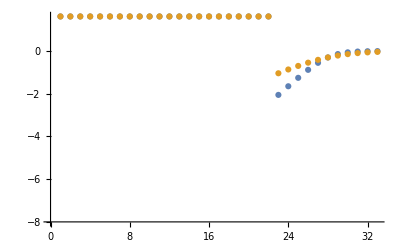

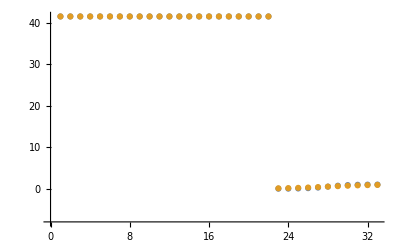

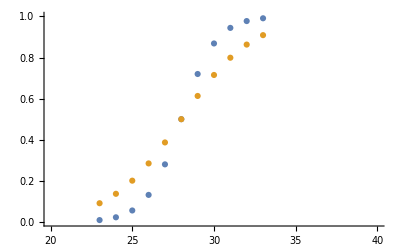

```mathematica
dataSet=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSet,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSet,3]]}, AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]], filteredDataList[[dataSet,3]]}, AxesOrigin->{0,-8}, PlotRange->{{20,40}, {0,1}}]
```

### Parameter Distribution



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```



```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 1.21792×10^-9
0.00089 | 0.00089 | 1.07241×10^-9
0.00053 | 0.00053 | 1.84462×10^-9

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 5.51572×10^-10

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 3.88996×10^-10

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.408 | 0.408 | 4.88403×10^-10

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
Needs["Toolbox`"];
Get["MASSef`"];
Get["MASSef`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
rxnName="FBP2";
fitLabel=rxnName;
dataFileName=rxnName;
KeqEquilibrator=2.4*10^-5;

(* user will need to change this path *)
pathMASSFittingPackage = "/home/mrama/Dropbox/test bla/MASSef/";

mainFolder = "test_refactor";
{workingDir, pathData, runFitScriptPath, inputPath, outputPath, bigg2equilibrator}=initializeNotebook[pathMASSFittingPackage,mainFolder];
```

/home/mrama/Dropbox/test bla/MASSef/data

Working dir:/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/

## Import Data

```mathematica
enzymeDataPath = FileNameJoin[{pathData, "kinetic_data_model.csv"}, OperatingSystem->$OperatingSystem];
bufferInfoDataPath = FileNameJoin[{pathData, "buffer_info.csv"}, OperatingSystem->$OperatingSystem];
ionChargeDataPath = FileNameJoin[{pathData, "ion_charge.csv"}, OperatingSystem->$OperatingSystem];

{rxn, mechanism, structure, nActiveSites, nAllostericSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}=getEnzymeData[rxnName, enzymeDataPath];

bufferInfo = getBufferInfoData[bufferInfoDataPath];
ionCharge = getIonData[ionChargeDataPath];

inhibitorMet={};
affectedMets={};(*There can be multiple metabolites*)
```

## Construct Module and Set Up Comparison Equations

### Print Module Dependent Information

```mathematica
printEnzymeData[rxn, mechanism, structure, nActiveSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(fdp^c+h2o^c→f6p^c+pi^c)^FBP2

;

Structure: 2

Active sites: 2

Km Values:

Substrate | Km_Value | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
fdp | 0.00007 |  | M | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004

S0.5 Values:

Substrate | S0.5_Value | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Metabolite(s) | Value | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
fdp | Null | 5.7 | 1/s | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004

Inhibition Values:

Parameter_Type | Inhibitor | Value | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
Ki | f6p | 0.001 |  | Competitive | Null | Null | Null | Null | M | 7.7 | 25 | tric | 0.02 | mn2 | 0.001
cl | 0.002
Ki | pi | 0.00035 |  | Competitive | Null | Null | Null | Null | M | 7.7 | 25 | tric | 0.02 | mn2 | 0.001
cl | 0.002

Activation Values:

Parameter_Type | Activator | Value | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Parameter_Type | Metabolite | Value | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Construct enzyme module

```mathematica
catalyticBranch={"E_FBP1[c] + fdp[c] <=> E_FBP1[c]&fdp",
				"E_FBP1[c]&fdp <=> E_FBP1[c]&f6p&pi",
				"E_FBP1[c]&f6p&pi <=> E_FBP1[c]&f6p + pi[c]",
				"E_FBP1[c]&f6p&pi <=> E_FBP1[c]&pi + f6p[c]",
				"E_FBP1[c]&f6p <=> E_FBP1[c] + f6p[c]",
				"E_FBP1[c]&pi <=> E_FBP1[c] + pi[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites-> 0];
```

### Setup King-Altmann Equations

```mathematica
{reverseZeroSub, forwardZeroSub, metSatForSub, metSatRevSub} = getMetsSub[rxn];
rates = getEnzymeRates[enzymeModel];
{KeqName, KeqVal, volumeSub} = getMisc[enzymeModel, rxnName];

(*competitiveRxns={};(*Initialization for later. Do not modify this*)
eqRateConstSub={};(*Initialization for later. Do not modify this*)*)

(*You could modify these, but you shouldn't unless you run into problems*)

lowerParamBound=-6;
upperParamBound=9;
simplifyMaxTime=1*^-5;

(*Extract Transition ID from Mass Action Equations and Separate Catalytic and Non-Catalytic Reactions*)
(*The transition indices are extracted based off of the sum of their mass action stoichiometry.Reactions with a sum of zero are assumed to be catalytic.*)

(*Separate Catalytic and Non-Catalytic Reactions*)
{allCatalyticReactions, nonCatalyticReactions}=classifyReactions[enzymeModel];


(*Identify Transition Rate Equations*)
transitionID =getTransitionIDs[allCatalyticReactions];

(*Extract Transition Rate Equations*)
transitionRateEqs=getTransitionRateEqs[transitionID, rates];

unifiedRateConstList=getUnifiedRateConstList[allCatalyticReactions, nonCatalyticReactions];


(* semi-automated add competitive inhibition steps - none in this enzyme*)
eqRateConstSub={};


(*King-Altman Workaround UsingMathematicaSolve*)
(*This section of code will check to see if there is a 'absoluteFlux.m' file in the notebook directory from a previous cell evalution, and it will either derive a generalized flux equation (may take a long time) or import the previously derived flux equation. Note: If you modify the binding mechanism used in the constructEnzymeModule or manually add additional reactions to the model, you should delete the 'absoluteFlux.m' file in this notebook's current directory.*)
absoluteFlux=getFluxEquation[inputPath, rxnName, enzymeModel, unifiedRateConstList, transitionRateEqs];


(*Equivalent Rate Constant Substitution for Random Ordered Mechanisms*)
(*This should work automatically,a substitution rule list is created with the name:'eqRateConstSub'.It is kind of a greedy section of code,so double check the results to make sure they're accurate*)
eqRateConstSub=getRateConstSubRandomMech[enzymeModel, eqRateConstSub, allCatalyticReactions, nonCatalyticReactions];

(*Assemble Kinetic MASS Action Comparision Equations that Match to Km and kcat Data*)
(*Simplify fixes Python evaluation issues dealing with fractional exponents (e.g.'(-1)**(3/5)' returns 1.0)*)
{absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse}=getRateEqs[absoluteFlux, unifiedRateConstList, eqRateConstSub, reverseZeroSub, forwardZeroSub, volumeSub, metSatForSub, metSatRevSub];


(*Assemble Rate Constant And Metabolite Substitutions for Export*)
{finalRateConsts,metsFull, metsSub, rateConstsSub}=getMetRatesSubs[enzymeModel, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse,KeqVal];

(*Export Equations*)
{eqnNameList, eqnValList, eqnValListPy, fileList, fileListSub}=exportRateEqs[inputPath, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, metsSub, metSatForSub, metSatRevSub, rateConstsSub];
```

## Semi-Automated Simulate Data

### User Input Section

```mathematica
logStepSize=0.2;
(*nonKmParamWeight=3;*)
(*Weighting factor for non-Km data points. You can be specify this manually*)
{minPsDataVal, maxPsDataVal}= getMinMaxPsDataVal[1];
nonKmParamWeight=Length[Table[1,{i,minPsDataVal, maxPsDataVal,logStepSize}]];
eTotal=1;(*Enzyme Total, Should Be 1 for Fitting*)
assumedSaturatingConc=0.01 ;(*in Molarity*)

(*Chemical Activity Correction Options*)
inVivoPH=7.5;(*Assumed in vivo pH*)
inVivoIS=0.25;(*Assumed in vivo Ionic Strength, in Molarity*)
effectiveIonDiameter=3;(*Used in Debye-Huckel equation, in Angstroms*)

(*Initialization of Chemical Activity Correction. These values represent no correction (i.e. Chemical Activity is just the Metabolite Concentration)*)
activeIsoSub=Thread[metsFull->metsFull];(*[S^z] = [S] *)
activityCoefficient=Thread[metsFull->1];(* γ = 1 *)
```

### Simulate data

```mathematica
pHandT={7.4,23};
kmFittingData= simulateKmData[rxn, metsFull,  metSatForSub, metSatRevSub, kmList, otherParmsList, assumedSaturatingConc, eTotal,
			   logStepSize,activeIsoSub, bufferInfo, ionCharge,  inputPath, fileList, KeqEquilibrator];

kcatFittingData=simulateKcatData[rxn, metsFull,  metSatForSub, metSatRevSub, kcatList, otherParmsList, assumedSaturatingConc, eTotal,
			  logStepSize, nonKmParamWeight, activeIsoSub, bufferInfo, ionCharge, inputPath, 
			  fileList, KeqEquilibrator];



haldane=haldaneRelation[KeqName,allCatalyticReactions]/.unifiedRateConstList;
haldaneRatio=haldane[[2]];

{KeqFittingData, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[haldaneRatio,KeqEquilibrator, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT,"haldaneRatio"];
```

### Sanity check plots

#### C inhib of dhap by glyc3p

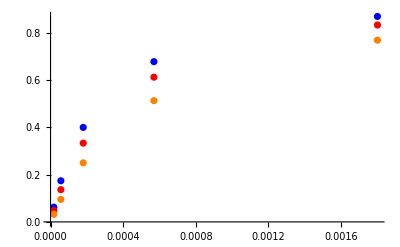

```mathematica
inhib1=inhibFittingData[[1;;5,{2,-1}]];
inhib2=inhibFittingData[[6;;10,{2,-1}]];
inhib3=inhibFittingData[[11;;15,{2,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.,0.00027}

{1.,0.00036}

{1.,0.00054}

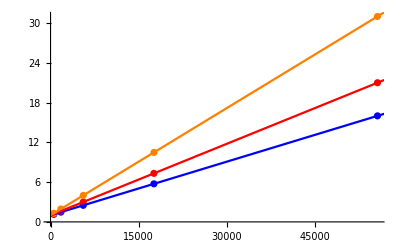

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,0,100000}, PlotStyle->{Blue,Red, Orange}]]
```

#### NC inhib of nadph by glyc3p

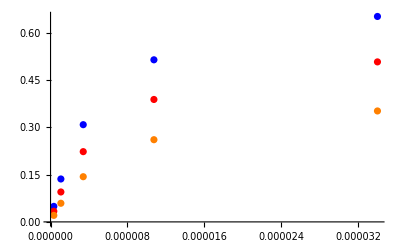

```mathematica
inhib1=inhibFittingData[[16;;20,{5,-1}]];
inhib2=inhibFittingData[[21;;25,{5,-1}]];
inhib3=inhibFittingData[[26;;30,{5,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.34615,6.46×10^-6}

{1.69231,9.52×10^-6}

{2.38462,0.00001564}

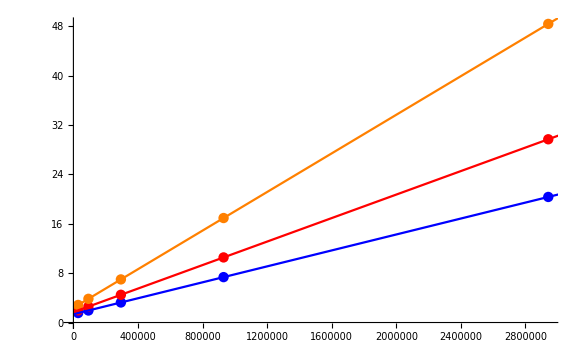

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

#### NC inhib of dhap by nadp

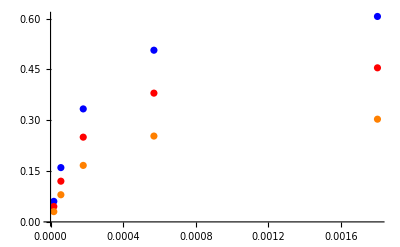

```mathematica
inhib1=inhibFittingData[[31;;35,{2,-1}]];
inhib2=inhibFittingData[[36;;40,{2,-1}]];
inhib3=inhibFittingData[[41;;45,{2,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.5,0.00027}

{2.,0.00036}

{3.,0.00054}

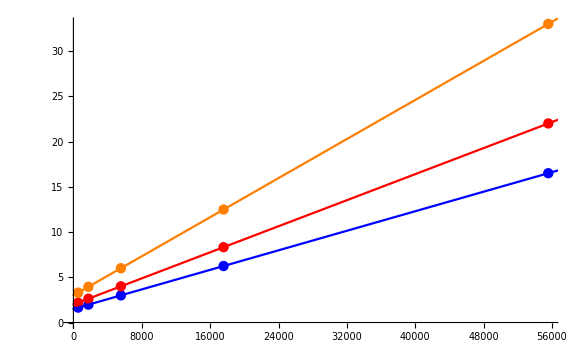

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

#### C inhib of nadph by nadp

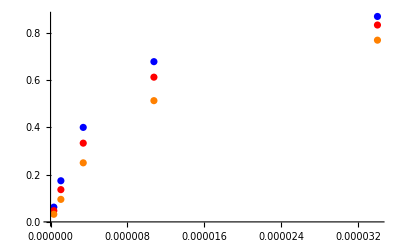

```mathematica
inhib1=inhibFittingData[[46;;50,{5,-1}]];
inhib2=inhibFittingData[[51;;55,{5,-1}]];
inhib3=inhibFittingData[[56;;60,{5,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.,5.1×10^-6}

{1.,6.8×10^-6}

{1.,0.0000102}

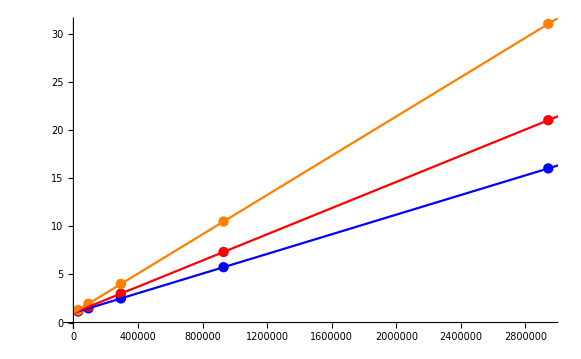

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

#### C inhib of glyc3p by dhap

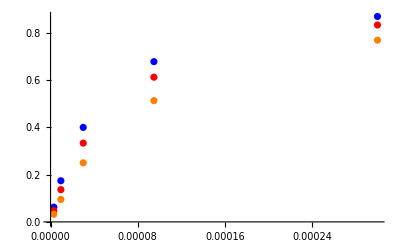

```mathematica
inhib1=inhibFittingData[[61;;65,{3,-1}]];
inhib2=inhibFittingData[[66;;70,{3,-1}]];
inhib3=inhibFittingData[[71;;75,{3,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.,0.000045}

{1.,0.00006}

{1.,0.00009}

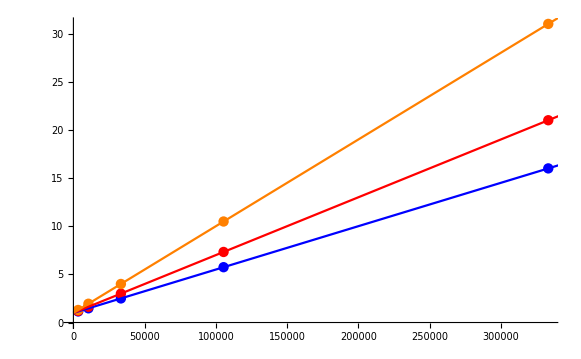

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

#### NC inhib of nadp by dhap

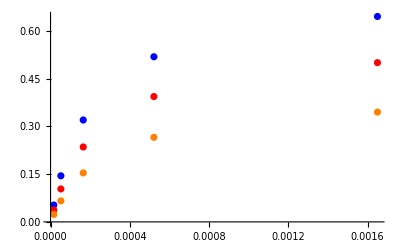

```mathematica
inhib1=inhibFittingData[[76;;80,{4,-1}]];
inhib2=inhibFittingData[[81;;85,{4,-1}]];
inhib3=inhibFittingData[[86;;90,{4,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.375,0.00028875}

{1.75,0.0004125}

{2.5,0.00066}

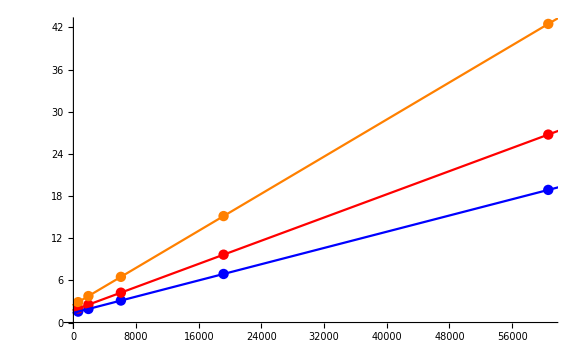

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

#### C inhib of nadp by nadph

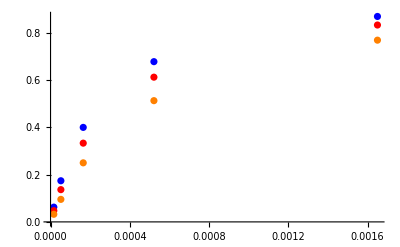

```mathematica
inhib1=inhibFittingData[[106;;110,{4,-1}]];
inhib2=inhibFittingData[[111;;115,{4,-1}]];
inhib3=inhibFittingData[[116;;120,{4,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.,0.0002475}

{1.,0.00033}

{1.,0.000495}

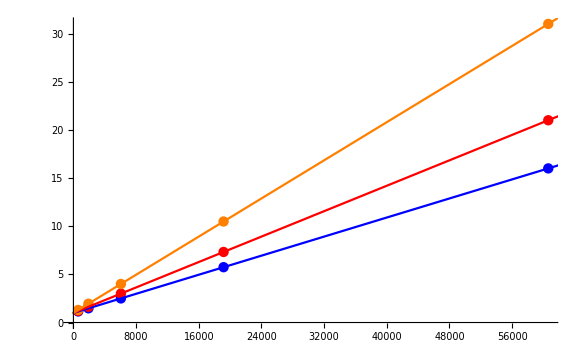

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

```mathematica
rxn
```

(glyc3p^c+nadp^c⇌dhap^c+h^c+nadph^c)^G3PD2

### Assemble and export All Data

```mathematica
header=Join[Map[ToString, metsSub[[All,1]]],{"FileFlag", "Target_Data"}];
fittingData = Flatten[{kmFittingData,kcatFittingData,KeqFittingData}, 1];

dataPath =FileNameJoin[{inputPath,dataFileName <>".dat"}, OperatingSystem->$OperatingSystem];

vList=Join[{header},fittingData];
Export[dataPath,vList,"Table"];
FilePrint[dataPath];
```

Keq_FBP2	f6p[c]	fdp[c]	pi[c]	param_FBP2_total	param_pH	param_Temp	FileFlag	Target_Data
0.000024	0	7.000000000000002e-6	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/relRateFor_fdp.txt"	0.09090909090909094
0.000024	0	0.000011094252347227801	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/relRateFor_fdp.txt"	0.13680688860321008
0.000024	0	0.00001758320502056708	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/relRateFor_fdp.txt"	0.20076000891310194
0.000024	0	0.000027867501938744792	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/relRateFor_fdp.txt"	0.2847472489508013
0.000024	0	0.000044167014113613516	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/relRateFor_fdp.txt"	0.3868631798468569
0.000024	0	0.00007000000000000002	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/relRateFor_fdp.txt"	0.5000000000000001
0.000024	0	0.00011094252347227801	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/relRateFor_fdp.txt"	0.6131368201531432
0.000024	0	0.0001758320502056708	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/relRateFor_fdp.txt"	0.7152527510491989
0.000024	0	0.0002786750193874482	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/relRateFor_fdp.txt"	0.7992399910868984
0.000024	0	0.0004416701411361352	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/relRateFor_fdp.txt"	0.86319311139679
0.000024	0	0.0007000000000000001	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/relRateFor_fdp.txt"	0.9090909090909092
0.000024	0	0.01	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/absRateFor.txt"	5.7
0.000024	0	0.01	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/absRateFor.txt"	5.7
0.000024	0	0.01	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/absRateFor.txt"	5.7
0.000024	0	0.01	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/absRateFor.txt"	5.7
0.000024	0	0.01	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/absRateFor.txt"	5.7
0.000024	0	0.01	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/absRateFor.txt"	5.7
0.000024	0	0.01	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/absRateFor.txt"	5.7
0.000024	0	0.01	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/absRateFor.txt"	5.7
0.000024	0	0.01	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/absRateFor.txt"	5.7
0.000024	0	0.01	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/absRateFor.txt"	5.7
0.000024	0	0.01	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/absRateFor.txt"	5.7
0.000024	0	0	0	1	7.4	23	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/haldaneRatio.txt"	0.000024
0.000024	0	0	0	1	7.4	23	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/haldaneRatio.txt"	0.000024
0.000024	0	0	0	1	7.4	23	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/haldaneRatio.txt"	0.000024
0.000024	0	0	0	1	7.4	23	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/haldaneRatio.txt"	0.000024
0.000024	0	0	0	1	7.4	23	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/haldaneRatio.txt"	0.000024
0.000024	0	0	0	1	7.4	23	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/haldaneRatio.txt"	0.000024
0.000024	0	0	0	1	7.4	23	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/haldaneRatio.txt"	0.000024
0.000024	0	0	0	1	7.4	23	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/haldaneRatio.txt"	0.000024
0.000024	0	0	0	1	7.4	23	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/haldaneRatio.txt"	0.000024
0.000024	0	0	0	1	7.4	23	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/haldaneRatio.txt"	0.000024
0.000024	0	0	0	1	7.4	23	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBP_Enzyme2/test_refactor/input/haldaneRatio.txt"	0.000024

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=1;
{psoParameterPath,psoResultsFileName, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFileName} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	1
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateRev_13dpg.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateRev_nadh.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateRev_13dpg.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateRev_nadh.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

### Run Fitting on your Local System

```mathematica
runFitScriptPath= FileNameJoin[{pathMASSFittingPackage <> "python_code","src", "run_fit_rel.py"}, OperatingSystem->$OperatingSystem];

runPythonCmd =StringRiffle[{"python","\""<>runFitScriptPath <>"\"", "\""<>psoParameterPath <>"\"", "\""<>lmaParameterPath <>"\"", "\""<>psoTrialSummaryFileName <>"\"","\""<> psoResultsFileName <>"\"", "\""<>lmaResultsFileName <>"\"", ToString @numTrials, "\""<>dataPath <>"\""}, " "];

runBothCmd="cd \""<>inputPath<>"\" && "<>runPythonCmd;
runBothExe="!"<>runBothCmd <>" 2>&1";

Import[runBothExe<>" 2>&1","Text"]
```

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
fittingData = Import[FileNameJoin[{inputPath, dataFileName<>".dat"}, OperatingSystem->$OperatingSystem]];
fittingData = fittingData[[2;;,All]];
resultsFile = FileNameJoin[{"raw","lmaResults_"<> fitLabel<> ".txt"}, OperatingSystem->$OperatingSystem];
flagFitType = "abs_ssd";

{flagFitLocal, msgLocal, filteredDataList, bestFitDetails}=getRatesWithSSD[resultsFile, rxnName, fittingData, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, {}, False,fitLabel];
```

```mathematica
bestFitDetails//TableForm
```

Fitting Equation | Relative error | True value | Predicted Value
 |  |  | 
prod_inhib_glyc3p | 52.0945 | 0.0625 | 0.0950591
prod_inhib_glyc3p | 40.4472 | 0.174112 | 0.244536
prod_inhib_glyc3p | 21.526 | 0.4 | 0.486104
prod_inhib_glyc3p | 3.9343 | 0.678269 | 0.704954
prod_inhib_glyc3p | 6.44477 | 0.869565 | 0.813524
prod_inhib_glyc3p | 74.6298 | 0.047619 | 0.083157
prod_inhib_glyc3p | 60.4322 | 0.136527 | 0.219033
prod_inhib_glyc3p | 35.8854 | 0.333333 | 0.452951
prod_inhib_glyc3p | 11.3432 | 0.612574 | 0.68206
prod_inhib_glyc3p | 3.55861 | 0.833333 | 0.803678
prod_inhib_glyc3p | 106.161 | 0.0322581 | 0.0665036
prod_inhib_glyc3p | 90.0551 | 0.0953577 | 0.181232
prod_inhib_glyc3p | 59.4337 | 0.25 | 0.398584
prod_inhib_glyc3p | 24.8053 | 0.513167 | 0.64046
prod_inhib_glyc3p | 2.00907 | 0.769231 | 0.784685
prod_inhib_glyc3p | 17.3592 | 0.0491493 | 0.0406174
prod_inhib_glyc3p | 23.9328 | 0.135972 | 0.10343
prod_inhib_glyc3p | 34.2924 | 0.308057 | 0.202417
prod_inhib_glyc3p | 43.486 | 0.513614 | 0.290264
prod_inhib_glyc3p | 48.3182 | 0.650976 | 0.336436
prod_inhib_glyc3p | 19.1964 | 0.0336788 | 0.0401439
prod_inhib_glyc3p | 5.90321 | 0.0948165 | 0.100414
prod_inhib_glyc3p | 14.1163 | 0.222603 | 0.19118
prod_inhib_glyc3p | 30.9937 | 0.387936 | 0.2677
prod_inhib_glyc3p | 39.5501 | 0.50702 | 0.306493
prod_inhib_glyc3p | 89.8089 | 0.0206677 | 0.0392292
prod_inhib_glyc3p | 60.643 | 0.0590629 | 0.0948805
prod_inhib_glyc3p | 20.1871 | 0.143172 | 0.172074
prod_inhib_glyc3p | 11.0517 | 0.260467 | 0.231681
prod_inhib_glyc3p | 25.9885 | 0.351541 | 0.260181
prod_inhib_nadp | 3.47733 | 0.0606061 | 0.0584986
prod_inhib_nadp | 5.05829 | 0.160169 | 0.152067
prod_inhib_nadp | 8.04581 | 0.333333 | 0.306514
prod_inhib_nadp | 12.4321 | 0.506498 | 0.44353
prod_inhib_nadp | 19.9952 | 0.606061 | 0.484877
prod_inhib_nadp | 8.6714 | 0.0454545 | 0.041513
prod_inhib_nadp | 5.44075 | 0.120127 | 0.113591
prod_inhib_nadp | 0.4384 | 0.25 | 0.251096
prod_inhib_nadp | 5.38268 | 0.379873 | 0.400321
prod_inhib_nadp | 2.0884 | 0.454545 | 0.464038
prod_inhib_nadp | 13.335 | 0.030303 | 0.0262621
prod_inhib_nadp | 5.82014 | 0.0800844 | 0.0754233
prod_inhib_nadp | 10.6473 | 0.166667 | 0.184412
prod_inhib_nadp | 32.2972 | 0.253249 | 0.335041
prod_inhib_nadp | 41.0117 | 0.30303 | 0.427308
prod_inhib_nadp | 40.3696 | 0.0625 | 0.037269
prod_inhib_nadp | 37.9254 | 0.174112 | 0.10808
prod_inhib_nadp | 32.3103 | 0.4 | 0.270759
prod_inhib_nadp | 23.8213 | 0.678269 | 0.516696
prod_inhib_nadp | 16.6341 | 0.869565 | 0.724921
prod_inhib_nadp | 22.7779 | 0.047619 | 0.0367724
prod_inhib_nadp | 21.805 | 0.136527 | 0.106757
prod_inhib_nadp | 19.5615 | 0.333333 | 0.268128
prod_inhib_nadp | 16.1481 | 0.612574 | 0.513655
prod_inhib_nadp | 13.2374 | 0.833333 | 0.723022
prod_inhib_nadp | 11.0355 | 0.0322581 | 0.0358179
prod_inhib_nadp | 9.28103 | 0.0953577 | 0.104208
prod_inhib_nadp | 5.20699 | 0.25 | 0.263017
prod_inhib_nadp | 1.06946 | 0.513167 | 0.507679
prod_inhib_nadp | 6.4971 | 0.769231 | 0.719253
prod_inhib_dhap | 16.055 | 0.0625 | 0.0524656
prod_inhib_dhap | 11.0709 | 0.174112 | 0.154837
prod_inhib_dhap | 0.669142 | 0.4 | 0.397323
prod_inhib_dhap | 4.73469 | 0.678269 | 0.710383
prod_inhib_dhap | 22.875 | 0.869565 | 0.670652
prod_inhib_dhap | 6.76662 | 0.047619 | 0.0508412
prod_inhib_dhap | 10.0636 | 0.136527 | 0.150267
prod_inhib_dhap | 16.1534 | 0.333333 | 0.387178
prod_inhib_dhap | 13.9675 | 0.612574 | 0.698136
prod_inhib_dhap | 20.1455 | 0.833333 | 0.665454
prod_inhib_dhap | 48.3384 | 0.0322581 | 0.0478511
prod_inhib_dhap | 48.7243 | 0.0953577 | 0.14182
prod_inhib_dhap | 47.2858 | 0.25 | 0.368215
prod_inhib_dhap | 31.4787 | 0.513167 | 0.674705
prod_inhib_dhap | 14.8179 | 0.769231 | 0.655247
prod_inhib_dhap | 51.0433 | 0.0529801 | 0.080023
prod_inhib_dhap | 40.9897 | 0.144739 | 0.204067
prod_inhib_dhap | 25.0869 | 0.32 | 0.400278
prod_inhib_dhap | 10.9132 | 0.518565 | 0.575157
prod_inhib_dhap | 3.44038 | 0.645161 | 0.667357
prod_inhib_dhap | 20.2507 | 0.0373832 | 0.0449535
prod_inhib_dhap | 20.5873 | 0.103566 | 0.124887
prod_inhib_dhap | 21.2629 | 0.235294 | 0.285325
prod_inhib_dhap | 22.085 | 0.393613 | 0.480542
prod_inhib_dhap | 22.6437 | 0.5 | 0.613219
prod_inhib_dhap | 0.354163 | 0.0235294 | 0.0234461
prod_inhib_dhap | 4.41757 | 0.0660105 | 0.0689265
prod_inhib_dhap | 15.8924 | 0.153846 | 0.178296
prod_inhib_dhap | 34.7323 | 0.265611 | 0.357863
prod_inhib_dhap | 52.2782 | 0.344828 | 0.525097
prod_inhib_nadph | 47.6586 | 0.0579011 | 0.0303062
prod_inhib_nadph | 44.9009 | 0.155173 | 0.0854986
prod_inhib_nadph | 39.6284 | 0.331034 | 0.199851
prod_inhib_nadph | 35.9221 | 0.515944 | 0.330606
prod_inhib_nadph | 43.6736 | 0.626632 | 0.352959
prod_inhib_nadph | 39.1148 | 0.0424779 | 0.0258627
prod_inhib_nadph | 39.0738 | 0.114592 | 0.0698166
prod_inhib_nadph | 39.3955 | 0.247423 | 0.149949
prod_inhib_nadph | 41.6259 | 0.390601 | 0.228009
prod_inhib_nadph | 48.9609 | 0.478088 | 0.244012
prod_inhib_nadph | 27.8389 | 0.0277136 | 0.0199984
prod_inhib_nadph | 32.1113 | 0.0752393 | 0.051079
prod_inhib_nadph | 39.1625 | 0.164384 | 0.100007
prod_inhib_nadph | 46.4805 | 0.262875 | 0.140689
prod_inhib_nadph | 53.481 | 0.324324 | 0.150872
prod_inhib_nadph | 141.203 | 0.0625 | 0.150752
prod_inhib_nadph | 91.145 | 0.174112 | 0.332807
prod_inhib_nadph | 34.6069 | 0.4 | 0.538428
prod_inhib_nadph | 1.34183 | 0.678269 | 0.669168
prod_inhib_nadph | 16.6453 | 0.869565 | 0.724824
prod_inhib_nadph | 89.3413 | 0.047619 | 0.0901625
prod_inhib_nadph | 65.9247 | 0.136527 | 0.226532
prod_inhib_nadph | 30.2633 | 0.333333 | 0.434211
prod_inhib_nadph | 0.177484 | 0.612574 | 0.611487
prod_inhib_nadph | 15.7435 | 0.833333 | 0.702138
prod_inhib_nadph | 54.9501 | 0.0322581 | 0.0499839
prod_inhib_nadph | 44.9725 | 0.0953577 | 0.138242
prod_inhib_nadph | 25.2127 | 0.25 | 0.313032
prod_inhib_nadph | 1.63757 | 0.513167 | 0.52157
prod_inhib_nadph | 14.0993 | 0.769231 | 0.660774

### Simulated Data and Best Fit Data Plot

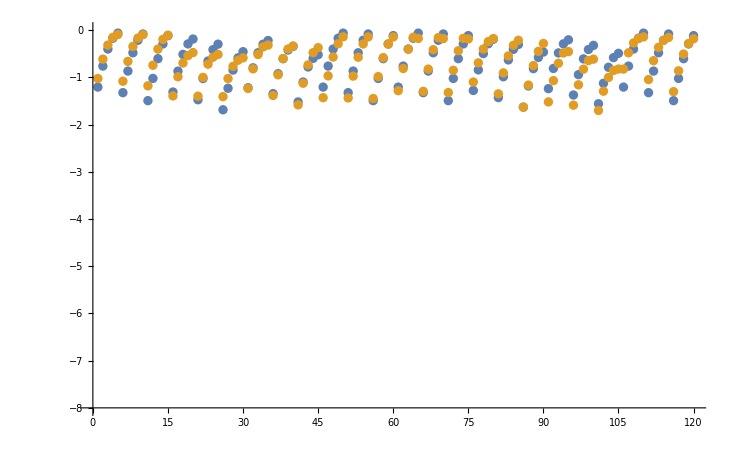

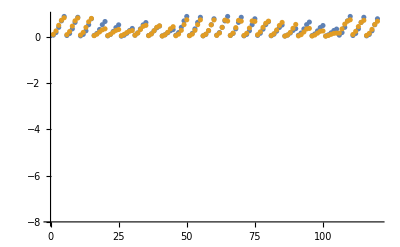

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

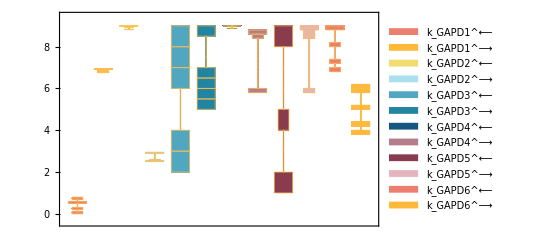

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

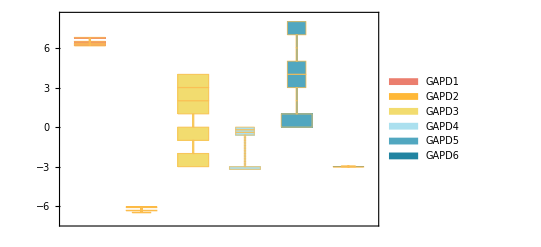

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

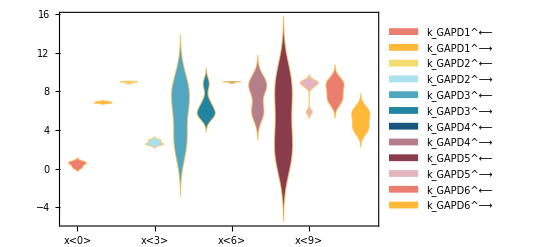

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[inputPath  <> "(.*)\\.txt"]->"$1"][[1]],{func,fittingData[[All,-2]]}];
```

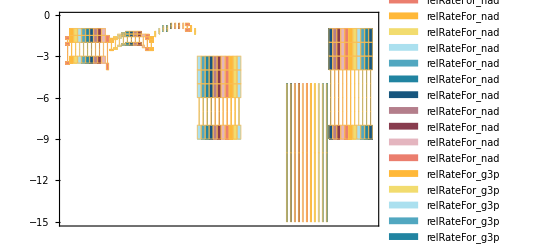

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> eTotal;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, KeqName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 1.46352×10^-10
0.00089 | 0.00089 | 1.3663×10^-9
0.00053 | 0.00053 | 2.89852×10^-9

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268. | 268. | 8.12479×10^-10

```mathematica
backCalculateRatios[dKdRatio, dKdVal, paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 4.86486×10^-10